# Équation d'onde classique

## Corde tendue fixée aux points x = 0 et x = L (Solution sous forme d’ondes stationnaire)

## Problème

Corde tendue de longueur L, de masse M, et de tension constante T fixée aux points x=0 et x=L ayant La forme initiale y(x) La vitesse initiale v(x).

### La masse de la corde (Kg)

```mathematica
M:=π
```

### Le longeure de la corde (m)

```mathematica
L:=π
```

### Le tension de la corde (N)

```mathematica
T:=100
```

On calcule la densité linéaire de la corde et la vitesse de propagation d'une onde sur la corde :

### La densité linéaire de la corde (Kgm^-1)

```mathematica
μ=M/L
```

1

### La vitesse de propagation d'une onde sur la corde (ms^-1)

```mathematica
v=√(T/μ)
```

10

## Équation d'onde

∂^2/(∂x^2)ψ(x,t)-1/v^2∂^2/(∂t^2)ψ(x,t)=0

### Les conditions frontières :

ψ (0, t) = 0
ψ (L, t) = 0

### Les conditions initiales :

#### La forme initiale de la corde :

```mathematica
y[x_]:=x(π-x)/π
```

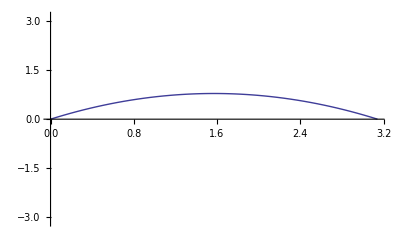

```mathematica
Plot[y[x],{x,0,L},PlotRange->{-L,L}]
```

#### La vitesse initiale de la corde (ms^-1) :

```mathematica
V[x_]:=0
```

## Solution de l'équation d^2/dx^2 X(x)+k^2 X(x)=0

### Les valeurs propres

```mathematica
Subscript[k, n_]=(n π)/L
```

n

### Les fonctions propres

```mathematica
Subscript[X, n_][x_]=Sin[Subscript[k, n]  x]
```

Sin[n x]

```mathematica
Table[Subscript[X, n][t],{n,1,6}]
```

{Sin[t],Sin[2 t],Sin[3 t],Sin[4 t],Sin[5 t],Sin[6 t]}

## Solution de l'équation d^2/dt^2 T(t)+ω^2 T(t)=0

### Les valeurs propres

```mathematica
Subscript[ω, n_]=Subscript[k, n] v
```

10 n

```mathematica
Table[Subscript[ω, n],{n,1,6}]
```

{10,20,30,40,50,60}

### Les coefficients de Fourier

```mathematica
Subscript[A, n_]=2/L ∫_0^L y[x]Sin[Subscript[k, n] x]ⅆx
```

(2 (2-2 Cos[n π]-n π Sin[n π]))/(n^3 π^2)

```mathematica
Table[Subscript[A, n],{n,1,6}]
```

{8/π^2,0,8/(27 π^2),0,8/(125 π^2),0}

```mathematica
Subscript[B, n_]=2/(n π v) ∫_0^L V[x]Sin[Subscript[k, n] x]ⅆx
```

0

```mathematica
Table[Subscript[B, n],{n,1,6}]
```

{0,0,0,0,0,0}

### Les fonctions propres

```mathematica
Subscript[T, n_][t_]=Subscript[A, n] Cos[(n π)/L v t]+Subscript[B, n] Sin[(n π)/L v t]
```

(2 Cos[10 n t] (2-2 Cos[n π]-n π Sin[n π]))/(n^3 π^2)

```mathematica
Table[Subscript[T, n][t],{n,1,6}]
```

{(8 Cos[10 t])/π^2,0,(8 Cos[30 t])/(27 π^2),0,(8 Cos[50 t])/(125 π^2),0}

## Les components de la fonction d'onde

```mathematica
Subscript[ψ, n_][x_,t_]=Subscript[X, n][x]Subscript[T, n][t]
```

(2 Cos[10 n t] (2-2 Cos[n π]-n π Sin[n π]) Sin[n x])/(n^3 π^2)

```mathematica
Table[Subscript[ψ, n][x,t],{n,1,6}]
```

{(8 Cos[10 t] Sin[x])/π^2,0,(8 Cos[30 t] Sin[3 x])/(27 π^2),0,(8 Cos[50 t] Sin[5 x])/(125 π^2),0}

```mathematica
table:=Table[{n,Subscript[ψ, n][x,t],Plot[Subscript[ψ, n][x,0],{x,0,L},Frame->True]},{n,1,6}]
```

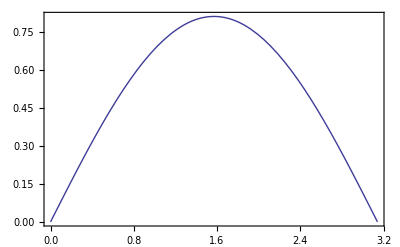
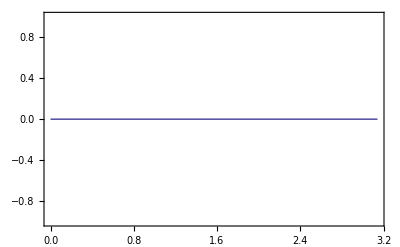
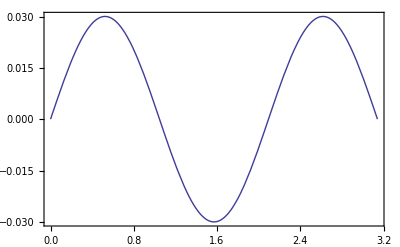
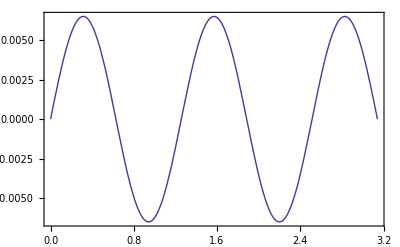
1 | (8 cos(10 t) sin(x))/π^2 | -Graphics-
2 | 0 | -Graphics-
3 | (8 cos(30 t) sin(3 x))/(27 π^2) | -Graphics-
4 | 0 | -Graphics-
5 | (8 cos(50 t) sin(5 x))/(125 π^2) | -Graphics-
6 | 0 | -Graphics-

```mathematica
Grid[table,Frame->All]//TraditionalForm
```

```mathematica
Manipulate[Plot[Subscript[ψ, n][x,t],{x,0,L},PlotRange->L,Frame->True],{n,{1,2,3,4,5,6}},{t,0,(4L)/v}]
```

## Solution Général

```mathematica
ψ[x_,t_]=∑_(n=1)^6 Subscript[ψ, n][x,t]
```

(8 Cos[10 t] Sin[x])/π^2+(8 Cos[30 t] Sin[3 x])/(27 π^2)+(8 Cos[50 t] Sin[5 x])/(125 π^2)

## Solution générale

```mathematica
Manipulate[Plot[∑_(n=1)^N Subscript[ψ, n][x,t],{x,0,L},PlotRange->L,Frame->True],{N,{3,6,12,18}},{t,0,(4L)/v}]
```